```mathematica
ClearAll["Global`*"];
dir=NotebookDirectory[];

data=Import[FileNameJoin[{dir,"output_TriangleParameterSubdivision"}]];
cleanData=data/.{s_String:>ToExpression[StringReplace[s,{"{"->"","}"->""}]]};
numericData=Partition[#,2]&/@cleanData;

dataTriangle2D=Import[FileNameJoin[{dir,"output_SubdivideSquareIntoTriangles2D"}]];
cleanData=dataTriangle2D/.{s_String:>ToExpression[StringReplace[s,{"{"->"","}"->""}]]};
numericDataTriangle2D=Partition[#,2]&/@cleanData;

dataTriangle3D=Import[FileNameJoin[{dir,"output_SubdivideSquareIntoTriangles3D"}]];
cleanData=dataTriangle3D/.{s_String:>ToExpression[StringReplace[s,{"{"->"","}"->""}]]};
numericDataTriangle3D=Partition[#,3]&/@cleanData;

dataSquareDomain=Import[FileNameJoin[{dir,"output_SquareParameterSubdivision"}]];
cleanData=dataSquareDomain/.{s_String:>ToExpression[StringReplace[s,{"{"->"","}"->""}]]};
numericDataSquareDomain=Partition[#,2]&/@cleanData;

dataMod=Import[FileNameJoin[{dir,"output_TriangleParameterSubdivision_Modified"}]];
cleanDataMod=dataMod/.{s_String:>ToExpression[StringReplace[s,{"{"->"","}"->""}]]};
numericDataMod=Partition[#,2]&/@cleanDataMod;
```

### 重心座標

```mathematica
Manipulate[
Graphics[
{Table[{EdgeForm[Thick],Opacity[0.5],Pink,Polygon[numericData[[i]]]},{i,1,max,1}],
,{Red,PointSize[Large],Point[{1/3,1/3}]}
}
,PlotRange->{{0,1},{0,1}}
,Frame->True
,FrameLabel->{Style["i",FontSlant->Italic,FontSize->20],Style["j",FontSlant->Italic,FontSize->20]}]
,{max,Length[numericData],1,-1}]
(*Export[FileNameJoin[{dir,"output_TriangleParameterSubdivision.gif"}],%]*)
```

```mathematica
Manipulate[
Graphics[
Table[{EdgeForm[Thick],Opacity[0.5],Pink,Polygon[numericDataTriangle2D[[i]]]},{i,1,max,1}]
,Axes->True]
,{max,Length[numericDataTriangle2D],1,-1}]
(*Export[FileNameJoin[{dir,"output_TriangleParameterSubdivision.gif"}],%]*)
```

```mathematica
Manipulate[
Graphics3D[Table[{EdgeForm[Thick],Opacity[0.5],Pink,Polygon[numericDataTriangle3D[[i]]]},{i,1,max,1}],
AxesOrigin->True,
Axes->True]
,{max,Length[numericDataTriangle3D],1,-1}]
(*Export[FileNameJoin[{dir,"output_TriangleParameterSubdivision.gif"}],%]*)
```

```mathematica
Manipulate[
Graphics[
Table[{EdgeForm[Thick],Opacity[0.5],Pink,Polygon[numericDataSquareDomain[[i]]]},{i,1,max,1}]
,PlotRange->{{0,1},{0,1}}
,Frame->True
,FrameLabel->{Style["i",FontSlant->Italic,FontSize->20],Style["j",FontSlant->Italic,FontSize->20]}]
,{max,Length[numericDataSquareDomain],1,-1}]
(*Export[FileNameJoin[{dir,"output_SquareParameterSubdivision.gif"}],%]*)
```

```mathematica
Manipulate[
Graphics[
{Table[{EdgeForm[Thick],Opacity[0.5],Pink,Polygon[numericDataMod[[i]]]},{i,1,max,1}](*,
,{Red,PointSize[Large],Point[{1/3,1/3}]}*)
}
,PlotRange->{{0,1},{0,1}}
,Frame->True
,FrameLabel->{Style["i",FontSlant->Italic,FontSize->20],Style["j",FontSlant->Italic,FontSize->20]}]
,{max,Length[numericDataMod],1,-1}]
(*Export[FileNameJoin[{dir,"output_SquareParameterSubdivision_into_Triangle.gif"}],%]*)
```

### 重心座標と線形の形状関数

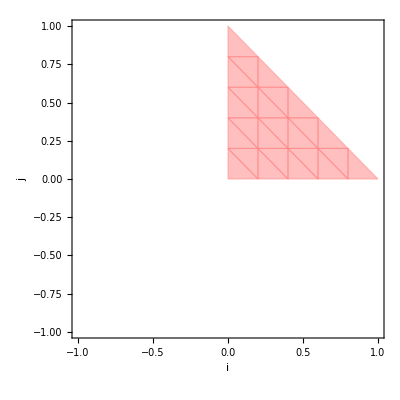
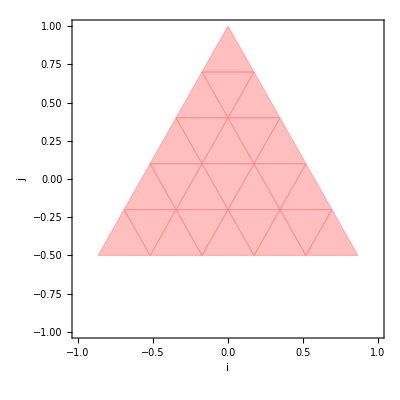
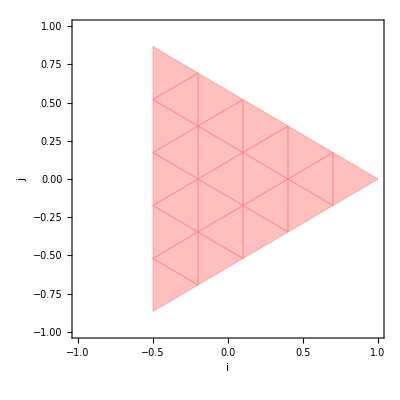

```mathematica
(*線形の形状関数は簡単に重心座標から作ることができ，形状関数は，３つのデータを三角形のように線形に繋ぐもの*)
shape[{t0_,t1_}]:={t0,t1,1-t0-t1};

vertexExample1={{1,0},{0,1},{0,0}};

{q0,q1,q2}={π/2,7π/6,11π/6};
vertexExample2={{Cos[q0],Sin[q0]},{Cos[q1],Sin[q1]},{Cos[q2],Sin[q2]}};

{q0,q1,q2}={π/2,7π/6,11π/6}+π/6;
vertexExample3={{Cos[q0],Sin[q0]},{Cos[q1],Sin[q1]},{Cos[q2],Sin[q2]}};

Table[
Module[{},
mapping[{a_,b_,c_}]:={Dot[shape[a],vertex],Dot[shape[b],vertex],Dot[shape[c],vertex]};
Graphics[
Table[{EdgeForm[Thick],Opacity[0.5],Pink,Polygon[mapping@numericData[[i]]]},{i,1,Length[numericData],1}]
,PlotRange->{{-1,1},{-1,1}}
,Frame->True
,FrameLabel->{Style["i",FontSlant->Italic,FontSize->20],Style["j",FontSlant->Italic,FontSize->20]}]
]
,{vertex,{vertexExample1,vertexExample2,vertexExample3}}]
```

```mathematica
dotsqrt[{x_,y_}]:=Sqrt[x*x+y*y];
shape[{t0_,t1_}]:={t0,t1,1-t0-t1};
{θ0,θ1,θ2}={π/2,7π/6,11π/6};
vertex={{Cos[θ0],Sin[θ0]},{Cos[θ1],Sin[θ1]},{Cos[θ2],Sin[θ2]}};
distance[t0_,t1_]:=Module[{w0,w1,w2,w3},
w0=FullSimplify[dotsqrt[Dot[shape[{t0,t1}],vertex]]];
w1=FullSimplify[dotsqrt[Dot[shape[{t0,t1}],vertex]-Dot[shape[{1/2,1/2}],vertex]]];
w2=FullSimplify[dotsqrt[Dot[shape[{t0,t1}],vertex]-Dot[shape[{-1/2,1/2}],vertex]]];
w3=FullSimplify[dotsqrt[Dot[shape[{t0,t1}],vertex]-Dot[shape[{1/2,-1/2}],vertex]]];
Return[{w0,w1,w2,w3}];
];

{θ0,θ1,θ2}={π/2,(7 π)/6,(11 π)/6};

Manipulate[Labeled[
Graphics[
{Table[{EdgeForm[Thick],Opacity[0.5],Pink,Polygon[Dot[{#1,#2,1-#1-#2}&@@@numericData[[i]],vertex]]},{i,1,max,1}]
,{Red,PointSize[Large],Point[Dot[shape[{1/3,1/3}],vertex]]}
,{Blue,PointSize[Large],Point[Dot[shape[{2/3,2/3}],vertex]]}
,{Green,PointSize[Large],Point[Dot[shape[{-1/3,2/3}],vertex]]}
,{Magenta,PointSize[Large],Point[Dot[shape[{2/3,-1/3}],vertex]]}
,{Red,Circle[Dot[shape[{1/3,1/3}],vertex],1]}
,{Blue,Circle[Dot[shape[{2/3,2/3}],vertex],1]}
,{Green,Circle[Dot[shape[{-1/3,2/3}],vertex],1]}
,{Magenta,Circle[Dot[shape[{2/3,-1/3}],vertex],1]}}
,PlotRange->{{-2,2},{-2,2}}
,Frame->True
,FrameLabel->{Style["i",FontSlant->Italic,FontSize->20],Style["j",FontSlant->Italic,FontSize->20]}]
,distance[t0,t1],Top]
,{max,Length[numericData],1,-1}
,{t0,0,1,0.01}
,{t1,0,1,0.01}]
```